#### Calibration trace at YOKO=0mA, 6.3~6.6GHz, 5dBm 10us integration 50Kavg,100KHz step

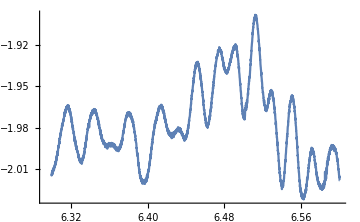
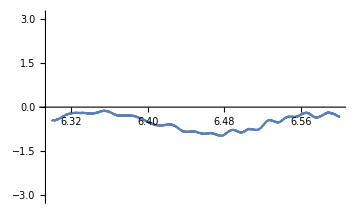

```mathematica
file="D:\\Travail Nath\\JQI\\branching_ratio_paper\\Data analysis package with 02 pumping\\one_tone_6.3GHz_to_6.6GHz_5dBm_0mA_10us integration_50Kavg_100KHz step_052518.dat";
data=Import[file];
header=Take[data,1];
ref=Drop[data,1];
edelay = 322.0;
ampref=ref[[;;,3]];
phaseref=ref[[;;,2]];
Row@{ListLinePlot[{#[[1]],Log10@#[[3]]}&/@ref,PlotRange->All,ImageSize->Medium],
ListLinePlot[{#[[1]],Arg[Exp[I(#[[2]]-edelay*#[[1]])]]}&/@ref,PlotRange->{-Pi,Pi},ImageSize->Medium]}
```

#### 0-1 Rabi 25dBm(Ch2) with reference@-0.60mA, with 0-2 pumping(10dBm 50us), (integration 1us, 500ns delay up to 500ns) at half flux quanta Pumping power do affeect decay of Rabi

```mathematica
file="D:\\TRAVAI~1\\JQI\\BRANCH~1\\DATAAN~1\\061218~1.H5";(*"/Users/admin_ncottet/Documents/nc/JQI/branching_ratio_paper/Data analysis package with 02 pumping/061218_Ch2 rabi 2Vpp_ Ch1 pumped_readout_6.5328GHz__-15dBm_qubit1.0105GHz_25dBm_pump_3.8366GHz_10dBm_-0.6_mA_I cos Q sin mod true interleafing_odd readout even ref_duty2us_1us read out_avg150k_to 1us.h5";*)
header=Import[file]
```

{/demod_Magnitude0,/demod_Phase0,/rabi_table}

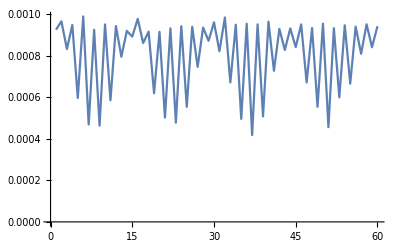

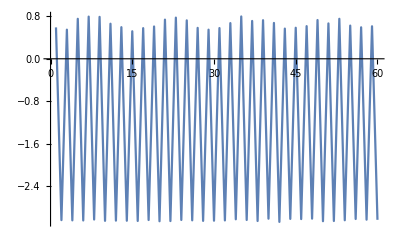

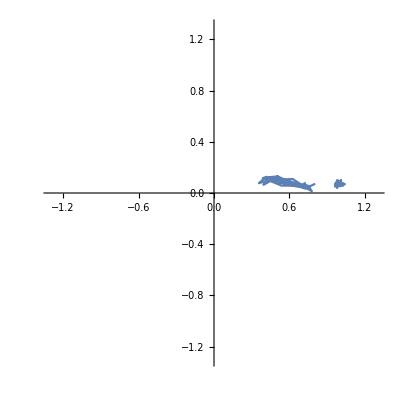

0.994083

{A→0.229387,B→0.569034,Ω→0.00405362,ϕo→-0.0101455,TR→2806.08}

123.347

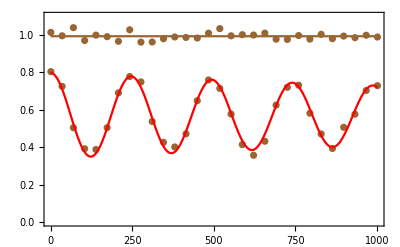

0.00591704

{A→0.229387,B→0.574951,Ω→0.00405362,ϕo→-0.0101455,TR→2806.08}

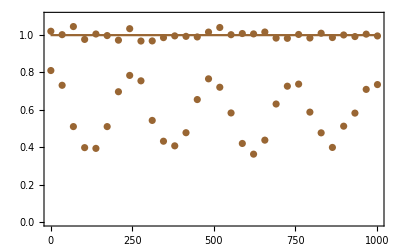

1.00595

{A→0.230752,B→0.572421,Ω→0.00405362,ϕo→-0.0101455,TR→2806.08}

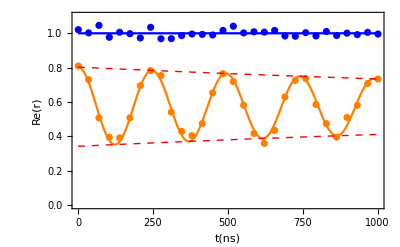

-0.039977

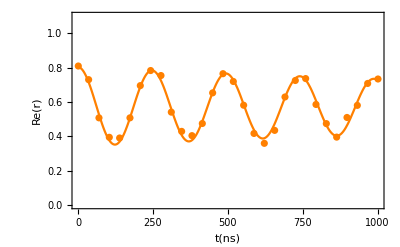

3.34472

0.658331

0.196827

-Graphics-

```mathematica
edelay1 = 322.;
edelay2 = 322.;
Freadout1=6.4828;
Freadout2 = 6.5828;
stepFreq=0.0001;
powerReadout=-15;
phaseoffset1=0.6π/2;
phaseoffset2 = -0.6π / 2;
powerRef=5;
numberloop =1;
numberRabidata =30;
refPoint1=IntegerPart[1+(Freadout1-6.3)/stepFreq];
refPoint2=IntegerPart[1+(Freadout2-6.3)/stepFreq];
delays = Flatten@Import[file,{"Datasets",3}];
amp=Flatten@Import[file,{"Datasets",1}];
ListLinePlot[amp]
tempamp = Table[amp[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempamp = Table[amp[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refamp = Flatten@Table[tempamp[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
phase=Flatten@Import[file,{"Datasets",2}];
ListLinePlot[phase]
For[i=1,i<numberloop*numberRabidata*2,i++,If[phase[[i]]>0,phase[[i]]=phase[[i]]-2*π,phase[[i]]=phase[[i]]]];
tempphase = Table[phase[[i]], {i, 1, numberRabidata*2*numberloop, 2}];
Rabiphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
tempphase = Table[phase[[i]], {i, 2, numberRabidata*2*numberloop, 2}];
Refphase = Flatten@Table[tempphase[[i+j*numberRabidata]],{j,0,(numberloop-1)}, {i,numberRabidata}];
Rabirefl2=10^(-(powerReadout-powerRef)/20)*Rabiamp*Exp[I*(Rabiphase-edelay1*Freadout1+phaseoffset1)]/ampref[[refPoint1]];
Refrefl2 = 10^(-(powerReadout-powerRef)/20)*Refamp*Exp[I*(Refphase-edelay2*Freadout2+phaseoffset2)]/ampref[[refPoint2]];
Show[ListLinePlot[Transpose@{Flatten@Re[Rabirefl2],Flatten@Im[Rabirefl2]},PlotRange->{{-1.3,1.3},{-1.3,1.3}}, AspectRatio->1],ListLinePlot[Transpose@{Flatten@Re[Refrefl2],Flatten@Im[Refrefl2]}]]
avgRef2=Mean[Re[Refrefl2]]
fit2=FindFit[Transpose[{delays,Re[Rabirefl2[[;;Length@delays]]]}],A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B,{{A,0.3},B,{Ω,0.004},{ϕo,0},{TR,1000}},t]
tπ=1/(2Ω)/.fit2
p02Rabi=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]},PlotRange->{0.0,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]},PlotRange->{0.0,1.3}, PlotStyle->Brown],Plot[avgRef2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Plot[A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B/.fit2,{t,0,delays[[-1]]}, PlotStyle->Red, PlotRange->All],Frame->True,LabelStyle->Medium]
shift2=1-avgRef2
shiftfit2=FindFit[Transpose[{delays,Re[Rabirefl2[[;;Length@delays]]]+shift2}],A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B,{{A,0.3},B,{Ω,0.004},{ϕo,0},{TR,1000}},t]
p02Rabishift=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]+shift2},PlotRange->{0.0,1.1}, PlotStyle->Brown],ListPlot[Transpose@{delays,Re[Refrefl2]+shift2},PlotRange->{-0.3,1.1}, PlotStyle->Brown],Plot[avgRef2+shift2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Brown],Frame->True,LabelStyle->Medium]
scale2=1/avgRef2
scalefit2=FindFit[Transpose[{delays,Re[Rabirefl2[[;;Length@delays]]]*scale2}],A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B,{{A,0.3},B,{Ω,0.004},{ϕo,0},{TR,1000}},t]
p2=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]*scale2},PlotRange->{0.0,1.1}, PlotStyle->Orange, LabelStyle->Large,FrameLabel->{t[ns],Re[r]}],ListPlot[Transpose@{delays,Re[Refrefl2]*scale2},PlotRange->{-0.2,1.2}, PlotStyle->Blue],Plot[avgRef2*scale2,{t,0,delays[[-1]]},PlotRange->All,PlotStyle->Blue],Plot[A*Cos[2π*Ω*t+ϕo]*Exp[-(t+ϕo)/TR]+B/.scalefit2,{t,0,delays[[-1]]}, PlotStyle->Orange, PlotRange->All],Plot[A*Exp[-t/TR]+B/.scalefit2,{t,0,delays[[-1]]}, PlotStyle->{Red, Dashed,Thick}, PlotRange->All], Plot[-A*Exp[-t/TR]+B/.scalefit2,{t,0,delays[[-1]]}, PlotStyle->{Red, Dashed,Thick}, PlotRange->All],Frame->True]
B2=B/.scalefit2;
A2=A/.scalefit2;
h=6.626*10^-34;
Teff=(h*1.006*10^9)/(-Log[(1-(B2-A2))/(1-(B2+A2))]*1.381*10^-23)

p2=Show[ListPlot[Transpose@{delays,Re[Rabirefl2]*scale2},PlotRange->{0.0,1.1}, PlotStyle->Orange, LabelStyle->Large,FrameLabel->{t[ns],Re[r]}],Plot[A*Cos[2π*Ω*t+ϕo]*Exp[-(t+ϕo)/TR]+B/.scalefit2,{t,0,delays[[-1]]}, PlotStyle->Orange, PlotRange->All],Frame->True]
Pratio01=(1-(B2-A2))/(1-(B2+A2))
(1-(B2-A2))
(1-(B2+A2))
P0ini=0.64;
r0=0.658;
p2=Show[ListPlot[Transpose@{delays/1000,(1-Re[Rabirefl2]*scale2)*(P0ini/r0)},PlotRange->{0.0,1.0}, PlotStyle->Automatic, PlotMarkers->{"●"},LabelStyle->Large,FrameLabel->{t[μs],P0}],Plot[(1-(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B))*(P0ini/r0)/.scalefit2,{t,0,delays[[-1]]/1000}, PlotStyle->Red, PlotRange->All],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.2i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
```

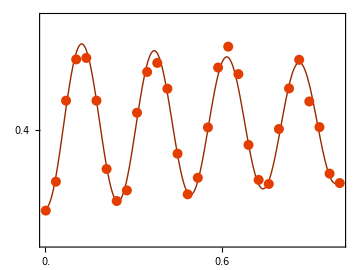

```mathematica
Show[Plot[(1-(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B))*(P0ini/r0)/.scalefit2,{t,0,delays[[-1]]/1000}, PlotStyle->Directive[Darker@RGBColor[0.89,0.24,0],Thick],PlotRange->{0.1,.7}],ListPlot[Transpose@{delays/1000,(1-Re[Rabirefl2]*scale2)*(P0ini/r0)}, PlotStyle->{PointSize[0.02],RGBColor[0.89,0.24,0]}],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.2i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

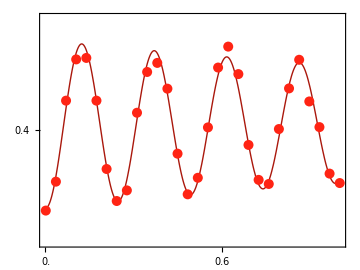

```mathematica
Show[Plot[(1-(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B))*(P0ini/r0)/.scalefit2,{t,0,delays[[-1]]/1000}, PlotStyle->Directive[Darker@RGBColor["#FF2414"],Thick],PlotRange->{0.1,.7}],ListPlot[Transpose@{delays/1000,(1-Re[Rabirefl2]*scale2)*(P0ini/r0)}, PlotStyle->{PointSize[0.02],RGBColor["#FF2414"]}],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.2i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```